```mathematica
ds=ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"];
```

```mathematica
ds[1]
```

```mathematica
ts=ds[1,"ConfirmedCases"]
```

TimeSeries[…]

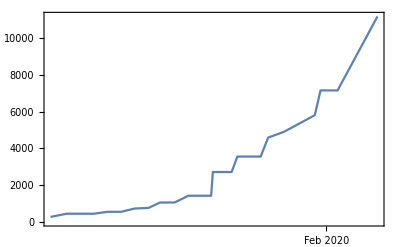

```mathematica
DateListPlot[ts]
```

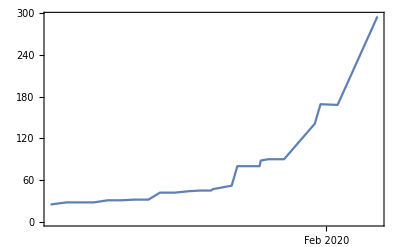

```mathematica
DateListPlot[ds[1,"RecoveredCases"],PlotRange->All]
```

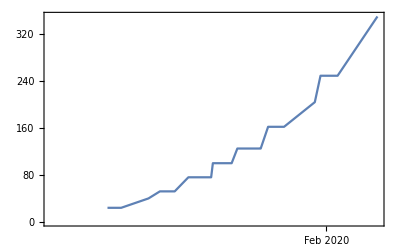

```mathematica
DateListPlot[ds[1,"Deaths"],PlotRange->All]
```

```mathematica
ds[1,"ConfirmedCases"]
```

TimeSeries[…]

```mathematica
ds[1,"ConfirmedCases"]["Values"]
```

{270,444,444,549,549,729,761,1052,1058,1423,1423,1423,2714,2714,3554,3554,3554,3554,4586,4903,5806,7153,7153,11177}

```mathematica
ds[1,"ConfirmedCases"]["Times"]
```

{3788632800,3788683200,3788769600,3788812800,3788856000,3788899200,3788942400,3788978400,3789025200,3789068400,3789104400,3789140400,3789145800,3789205200,3789223200,3789241200,3789293400,3789297000,3789320400,3789370800,3789468000,3789486000,3789540000,3789666000}

```mathematica
ds[1,"ConfirmedCases"]["Dates"]
```

{Tue 21 Jan 2020 22:00:00GMT-6.,Wed 22 Jan 2020 12:00:00GMT-6.,Thu 23 Jan 2020 12:00:00GMT-6.,Fri 24 Jan 2020 00:00:00GMT-6.,Fri 24 Jan 2020 12:00:00GMT-6.,Sat 25 Jan 2020 00:00:00GMT-6.,Sat 25 Jan 2020 12:00:00GMT-6.,Sat 25 Jan 2020 22:00:00GMT-6.,Sun 26 Jan 2020 11:00:00GMT-6.,Sun 26 Jan 2020 23:00:00GMT-6.,Mon 27 Jan 2020 09:00:00GMT-6.,Mon 27 Jan 2020 19:00:00GMT-6.,Mon 27 Jan 2020 20:30:00GMT-6.,Tue 28 Jan 2020 13:00:00GMT-6.,Tue 28 Jan 2020 18:00:00GMT-6.,Tue 28 Jan 2020 23:00:00GMT-6.,Wed 29 Jan 2020 13:30:00GMT-6.,Wed 29 Jan 2020 14:30:00GMT-6.,Wed 29 Jan 2020 21:00:00GMT-6.,Thu 30 Jan 2020 11:00:00GMT-6.,Fri 31 Jan 2020 14:00:00GMT-6.,Fri 31 Jan 2020 19:00:00GMT-6.,Sat 1 Feb 2020 10:00:00GMT-6.,Sun 2 Feb 2020 21:00:00GMT-6.}

```mathematica
UnixTime[]
```

1580935583

```mathematica
AbsoluteTime[]//Round
```

3789902796

```mathematica
FindFit[ds[1,"ConfirmedCases"],a x+b,{a,b},x]
```

{a→0.00912366,b→-3.45678×10^7}

#### analysis #1 -- quadratic fit

```mathematica
FindFit[ds[1,"ConfirmedCases"],a x^2+b x+c,{a,b,c},x]
```

{a→1.26536×10^-8,b→-95.8828,c→1.81639×10^11}

```mathematica
eqn=a x^2+b x+c/.{a->1.2653553653937558*^-8,b->-95.88279818931666,c->1.816389146070655*^11}
```

1.81639×10^11-95.8828 x+1.26536×10^-8 x^2

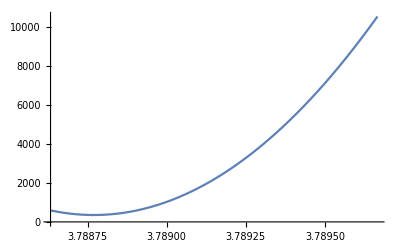

```mathematica
p1=Plot[eqn,{x,3788632800,3789666000}]
```

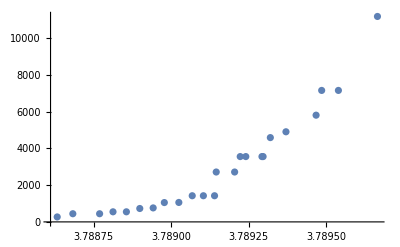

```mathematica
p2=ListPlot[Transpose[ds[1,"ConfirmedCases"][#]&/@{"Times","Values"}]]
```

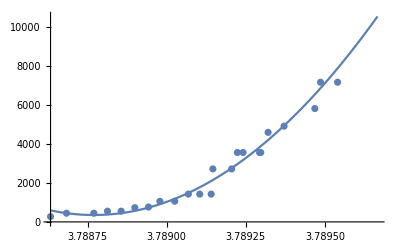

```mathematica
Show[p1,p2]
```

#### analysis #2 -- exponential fit

```mathematica
24 60 60
```

86400

```mathematica
times=(ds[1,"ConfirmedCases"]["Times"]-3788632800)/86400.
```

{0.,0.583333,1.58333,2.08333,2.58333,3.08333,3.58333,4.,4.54167,5.04167,5.45833,5.875,5.9375,6.625,6.83333,7.04167,7.64583,7.6875,7.95833,8.54167,9.66667,9.875,10.5,11.9583}

```mathematica
{min,max}=MinMax[times]
```

{0.,11.9583}

```mathematica
values=ds[1,"ConfirmedCases"]["Values"]
```

{270,444,444,549,549,729,761,1052,1058,1423,1423,1423,2714,2714,3554,3554,3554,3554,4586,4903,5806,7153,7153,11177}

```mathematica
data=Transpose[{times,values}]
```

{{0.,270},{0.583333,444},{1.58333,444},{2.08333,549},{2.58333,549},{3.08333,729},{3.58333,761},{4.,1052},{4.54167,1058},{5.04167,1423},{5.45833,1423},{5.875,1423},{5.9375,2714},{6.625,2714},{6.83333,3554},{7.04167,3554},{7.64583,3554},{7.6875,3554},{7.95833,4586},{8.54167,4903},{9.66667,5806},{9.875,7153},{10.5,7153},{11.9583,11177}}

```mathematica
FindFit[data,a Exp[k t],{a,k},t]
```

{a→442.4,k→0.271635}

```mathematica
eqn=a Exp[k t]/.{a->442.40001904795184,k->0.3143920658265664}
```

442.4 ⅇ^(0.314392 t)

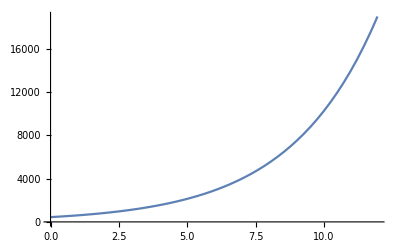

```mathematica
p1=Plot[eqn,{t,min,max}]
```

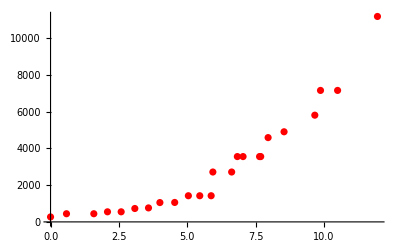

```mathematica
p2=ListPlot[data,PlotStyle->Red]
```

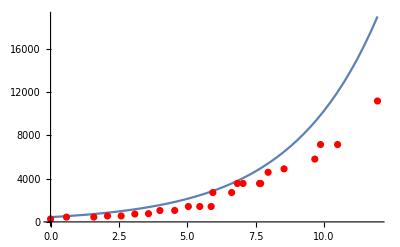

```mathematica
Show[p1,p2]
```